```mathematica
f[x_,y_]:=(10^(-3x)-1+(1-10^x)^5)*y
dfy = D[f[x,y],{y,2}]
dfx = D[f[x,y],{x,2}]
```

0

y (-2^x 5^(1+x) (1-10^x)^4 Log[2] Log[10]-2^x 5^(1+x) (1-10^x)^4 Log[5] Log[10]+9 10^(-3 x) Log[10]^2+2^(2+2 x) 5^(1+2 x) (1-10^x)^3 Log[10]^2)

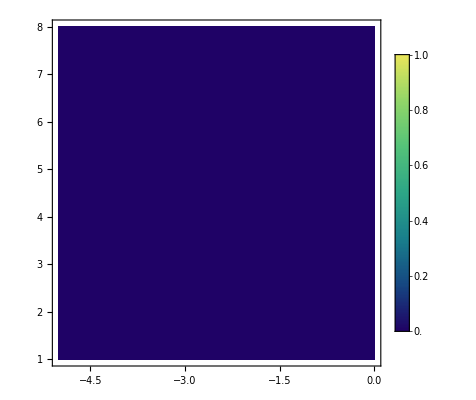

```mathematica
DensityPlot[dfy,{x,-5,-0.0001},{y,1,8},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic]
```

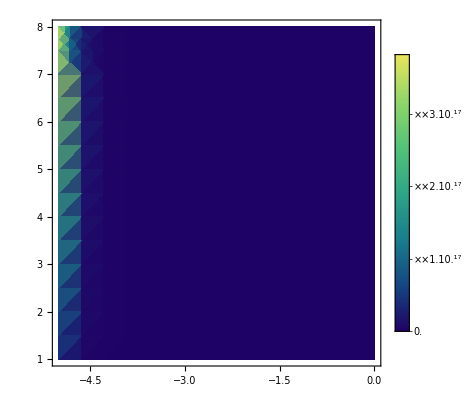

```mathematica
DensityPlot[dfx,{x,-5,-0.0001},{y,1,8},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,PlotRange->All]
```